```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../FA_models/SMS-stop-SMQCD-NLO_FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles}];
```

## Top Self Energy

### Remove diagrams which are identically zero due to color conservation

generic model {Lorentz} initialized

classes model {../../FA_models/SMS-stop-SMQCD-NLO_FA} initialized

in total: 2 Particles insertions

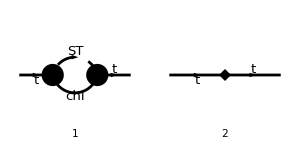

FeynArtsGraphics({t}→{t})(([1] | [2]))

```mathematica
tops = CreateTopologies[1, 1->1,  ExcludeTopologies -> {TadpoleCTs,Tadpoles}];
topsCT = CreateCTTopologies[1,1->1];
processTT =  { F[3]} -> {F[3]};
allDiags = InsertFields[Join[tops,topsCT],processTT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],V[2],V[3],V[4]}];
goodDiags = allDiags;
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 300,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True]
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]/.{FR$deltaZ[{t,t},{{}},"L"]->deltaZL,FR$deltaZ[{t,t},{{}},"R"]->deltaZR,FR$delta[{MT},{}]->deltaM}
```

in total: 2 Particles amplitudes

-((-ⅈ yDM (γ̄)^7 δ_Col1Col2).(mChi+γ·q).(-ⅈ yDM (γ̄)^6))/((q^2-mChi^2).((q-p)^2-mST^2))-ⅈ deltaZL δ_Col1Col2 (-(γ·p)).(γ̄)^7+ⅈ deltaZR δ_Col1Col2 (γ·p).(γ̄)^6-1/2 ⅈ δ_Col1Col2 (2 deltaM+deltaZL MT+deltaZR MT)

```mathematica
(* Replace the momenta to simplify the results *)
ampB =FullSimplify[SUNSimplify[DiracSimplify[FCReplaceMomenta[ampA,{p2->p23-p3,p1->p13-p3}]]]]
```

-1/2 ⅈ δ_Col1Col2 ((2 ⅈ yDM^2 (γ·q).(γ̄)^6)/((q^2-mChi^2).((p-q)^2-mST^2))-2 deltaZL (γ·p).(γ̄)^7-2 deltaZR (γ·p).(γ̄)^6+2 deltaM+MT (deltaZL+deltaZR))

```mathematica
ampC = TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->False]//Simplify
```

-1/2 ⅈ δ_Col1Col2 (-2 (γ·p).(γ̄)^6 (deltaZR-π^2 yDM^2 B_1(p^2,mChi^2,mST^2))-2 deltaZL (γ·p).(γ̄)^7+2 deltaM+deltaZL MT+deltaZR MT)

```mathematica
Expand[ampC]
```

-ⅈ π^2 yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6 B_1(p^2,mChi^2,mST^2)+ⅈ deltaZL δ_Col1Col2 (γ·p).(γ̄)^7+ⅈ deltaZR δ_Col1Col2 (γ·p).(γ̄)^6-ⅈ deltaM δ_Col1Col2-1/2 ⅈ deltaZL MT δ_Col1Col2-1/2 ⅈ deltaZR MT δ_Col1Col2

## Renormalization Conditions

```mathematica
sub={PaVe[1,{Pair[Momentum[p,D],Momentum[p,D]]},{mChi^2,mST^2},__]->B1[psq]};
onShell={psq->MT^2};
fL=Coefficient[Expand[ampC],DiracGamma[Momentum[p,D],D].DiracGamma[7]]/.sub
fR=Coefficient[Expand[ampC],DiracGamma[Momentum[p,D],D].DiracGamma[6]]/.sub
fSL=Select[Expand[ampC],FreeQ[#,DiracGamma,Infinity]&]/.sub (* Since the term without gamma equals PL+PR *)
fSR=Select[Expand[ampC],FreeQ[#,DiracGamma,Infinity]&]/.sub(* Since the term without gamma equals PL+PR *)
```

ⅈ deltaZL δ_Col1Col2

ⅈ deltaZR δ_Col1Col2-ⅈ π^2 yDM^2 B1(psq) δ_Col1Col2

-ⅈ deltaM δ_Col1Col2-1/2 ⅈ deltaZL MT δ_Col1Col2-1/2 ⅈ deltaZR MT δ_Col1Col2

-ⅈ deltaM δ_Col1Col2-1/2 ⅈ deltaZL MT δ_Col1Col2-1/2 ⅈ deltaZR MT δ_Col1Col2

```mathematica
eq1:=((MT fL+fSR)/.onShell)==0;
eq2:=((MT fR+fSL)/.onShell)==0;
eq3:=((2 MT D[MT(fL+fR)+fSL+fSR,psq]+fL+fR)/.onShell)==0;
```

```mathematica
solutionCTs=FullSimplify[Solve[{eq1,eq2,eq3},{deltaM,deltaZL,deltaZR}]][[1]]
```

{deltaM→-1/2 π^2 MT yDM^2 B1(MT^2),deltaZL→π^2 MT^2 yDM^2 B1'(MT^2),deltaZR→π^2 yDM^2 (MT^2 B1'(MT^2)+B1(MT^2))}

## Check Against Analytical Results

```mathematica
b1=Simplify[PaXEvaluate[B1[MT^2,mChi^2,mST^2],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)]/.{1/Epsilon->EulerGamma-Log[4 Pi],ScaleMu->mST}];
db1=Simplify[D[b1/.{MT-> √psq},psq]/.{psq->MT^2}];
deltaSPsol=1/(I Pi^2 yDM^2)(I deltaZR)/.solutionCTs/.{B1[MT^2]->Re[b1],Derivative[1][B1][MT^2]->Re[db1]};
deltaSsol=1/(I Pi^2 yDM^2)(-I MT deltaZL)/.solutionCTs/.{B1[MT^2]->Re[b1],Derivative[1][B1][MT^2]->Re[db1]};
```

```mathematica
lA=1+xC^2+xT^2-2*xC-2*xT-2*xT*xC;
xC = mChi^2/mST^2;
xT=MT^2/mST^2;
lB=-lA;
deltaS1=(-mST/(32*Pi^4*xT^(3/2)))*(xT*(2*xC+xT-2)+(-xC^2+2*xC+xT-1)*Log[xC]-2*(-xC^3+(3+xT)*xC^2+(xT-3)*xC+(xT-1)^2)*Log[(xC-xT+Sqrt[lA]+1)/(2*Sqrt[xC])]/(Sqrt[lA]));
deltaSP1=(1/(64*Pi^4*xT^2))*(2*xT*(xC-xT-1)+(-xC^2+2*xC+xT^2-1)*Log[xC]+2*(xC^3-(3+xT)*xC^2+(xT^2+3)*xC-(xT+1)*(xT-1)^2)*Log[(xC-xT+Sqrt[lA]+1)/(2*Sqrt[xC])]/(Sqrt[lA]));
deltaS2=(-mST/(32*Pi^4*xT^(3/2)))*(xT*(xC-1)+xT*(xC+xT-1)-Sqrt[lB]*(xC-1)*ArcTan[Sqrt[lB]/(1+xC-xT)]+(xC+xT-1)*(xC^2-(2+xT)*xC-xT+1)*ArcTan[Sqrt[lB]/(1+xC-xT)]/Sqrt[lB]-(xC^2-2*xC-xT+1)*Log[xC]);
deltaSP2=(2/(64*Pi^4*xT^2))*(-2*xT^2+xT*(xC+xT-1)+Sqrt[lB]*xT*ArcTan[Sqrt[lB]/(1+xC-xT)]+(xC+xT-1)*(xC^2-(xT+2)*xC-xT+1)*ArcTan[Sqrt[lB]/(1+xC-xT)]/Sqrt[lB]-(xC^2-2*xC-xT^2+1)*Log[xC]/2);
```

```mathematica
FullSimplify[deltaSP1-deltaSPsol,Assumptions->{MT>0,mST>0,mChi>0,mST>mChi+MT}]
FullSimplify[deltaS1-deltaSsol,Assumptions->{MT>0,mST>0,mChi>0,mST>mChi+MT}]
```

0

0

The region with an imaginary part needs to be checked numerically :

```mathematica
deltaSP2/.{mST->800.,mChi->700,MT->173.}
deltaSPsol/.{mST->800.,mChi->700,MT->173.}
deltaS2/.{mST->800.,mChi->700,MT->173.}
deltaSsol/.{mST->800.,mChi->700,MT->173.}
```

-0.0000322656

-0.0000322656

0.000483713

0.000483713